```mathematica
data=Import[NotebookDirectory[]<>"..\\..\\data\\2020_Problem_D_DATA\\passingevents.csv"];
```

```mathematica
object=Transpose[data][[{1,2,3,4}]];
```

```mathematica
allmember={"Huskies_D1","Huskies_F1","Huskies_M1","Huskies_F2","Huskies_M2","Huskies_M3","Huskies_G1","Huskies_D2","Huskies_D3","Huskies_D4","Huskies_F3","Huskies_D5","Huskies_M4","Huskies_M5","Huskies_D6","Huskies_M6","Huskies_M7","Huskies_M8","Huskies_M9","Huskies_F4","Huskies_D7","Huskies_M10","Huskies_M11","Huskies_M12","Huskies_M13","Huskies_F5","Huskies_F6","Huskies_D8","Huskies_D9","Huskies_D10"};
```

```mathematica
myteam=Drop[Thread[Table[object[[i]],{i,1,4}]],1];
```

```mathematica
member2=Subsets[allmember,{2}];
```

```mathematica
allteam=Drop[Thread[Table[object[[i]],{i,1,4}]],1];
```

```mathematica
WonderfulFunction[person1_,person2_,match_]:={
allteamfnmatch1=Cases[myteam,{match,_,_,_}];
allteamfnmatch1fn1=Drop[#,2]&/@allteamfnmatch1;
allteamfnmatch1fn2=Drop[Flatten@allteamfnmatch1fn1,1];
chuli1=Partition[allteamfnmatch1fn2,2]//PositionIndex;
samecase=Cases[Keys[chuli1],{x_,x_}];
numberlist=Table[
chuli1[samecase[[i]]],{i,1,samecase//Length}]//Flatten//Sort;
continuationnumber=Split[numberlist,(#2-#1==1&)]/.{_}->Nothing;
continuationnumbernew=Append[Prepend[#,#[[1]]-1],#[[-1]]+1]&/@continuationnumber;
result=Table[Flatten@Position[chuli1,#[[i]]]//First//First//First,{i,1,Length@#}]&/@continuationnumbernew;
resultunion=Union/@result;
Histogram[Length@#&/@resultunion]};
```

```mathematica
member2//Length
```

435

First::nofirst: {} 长度为零，没有第一个元素.

General::stop: 在本次计算中，First::nofirst 的进一步输出将被抑制.

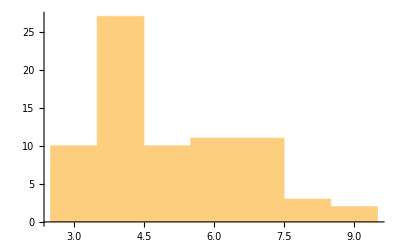
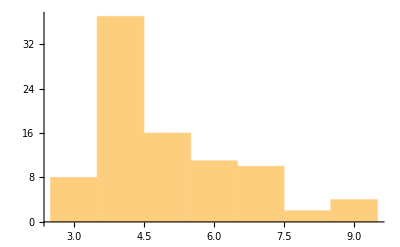
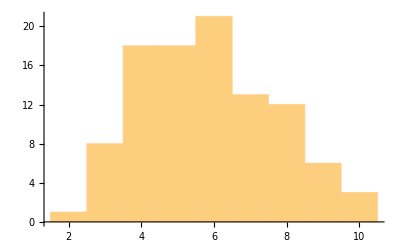
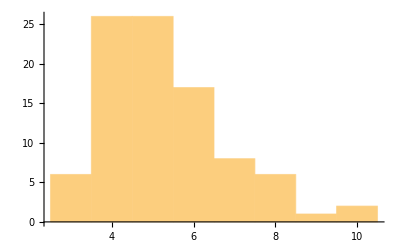
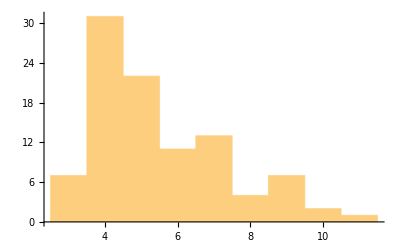
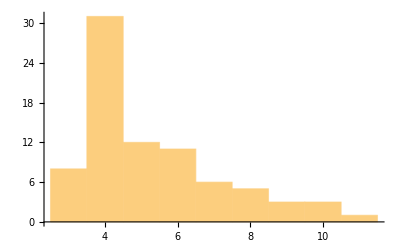
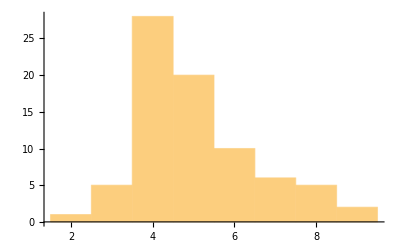
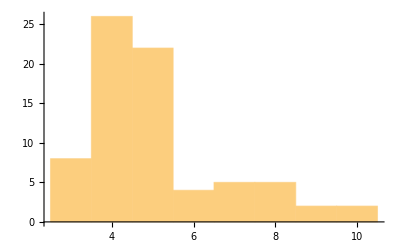

```mathematica
Table[WonderfulFunction["Huskies_D1","Huskies_F1",i],{i,1,38}]
```

```mathematica
WonderfulFunction[#1,#2,1]&@@@member2
```

{{0},{{2/3}},{{1/3}},{0},{0},{0},{{1/6}},{{1/6,1/3}},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{{1/3,1/6}},{0},{0},{0},{0},{{1/3}},{0},{0},{0},{0},{{1/6}},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{{1/2}},{0},{0},{0},{0},{{1/6}},{{1/6}},{{1/6}},{{1/6}},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{{1/6}},{{1/6}},{0},{{1/6}},{{1/6}},{{1/6}},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{{1}},{{1,1/3}},{{1/3}},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{{1/3,1}},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{{1/3}},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
WonderfulFunction[#1,#2,2]&@@@member2
```

{{0},{{1/8}},{0},{0},{{1/8}},{0},{{1,1/8}},{{1}},{0},{0},{0},{0},{0},{{1/8}},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{{1/8}},{0},{0},{0},{{1/8}},{0},{0},{0},{0},{0},{0},{{1/8}},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{{1/8}},{{1/8}},{0},{0},{0},{0},{0},{0},{{1/8}},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{{1/2}},{{1/2}},{0},{0},{0},{0},{{1/8}},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{{1/8}},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{{1}},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{{1/2}},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

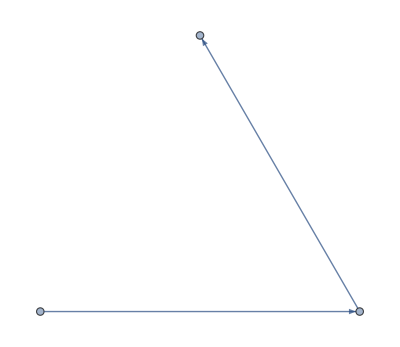
<|-Graphics-→6,-Graphics-→3,-Graphics-→1|>

```mathematica
myteamtrueskillpattern
```

```mathematica
continuousskilllist
```

{{Huskies_D2,Huskies_D3,Huskies_G1,Huskies_D3},{Huskies_D3,Huskies_D4,Huskies_D3,Huskies_G1}}

```mathematica
memberskilltimes
```

{1,1}

```mathematica
(Identity@@Select[Normal@myteamtrueskillpattern,IsomorphicGraphQ[patternmemberskill[[1]],(#)[[1]]]&])[[2]]
```

1

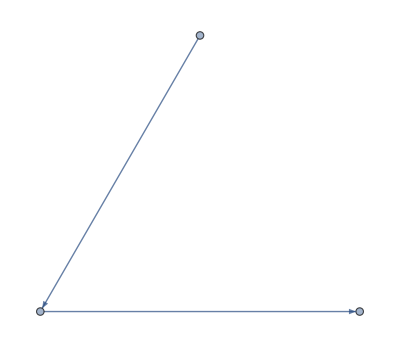

```mathematica
test={<|-Graphics-->6,-Graphics-->3,-Graphics-->1|>,<|-Graphics-->8,-Graphics-->1|>,<|-Graphics-->8,-Graphics-->1|>,<|-Graphics-->4,-Graphics-->2,-Graphics-->2,-Graphics-->1|>,<|-Graphics-->6,-Graphics-->1,-Graphics-->1|>,<|-Graphics-->7,-Graphics-->2,-Graphics-->1|>,<|-Graphics-->19,-Graphics-->3,-Graphics-->3,-Graphics-->2,-Graphics-->1,-Graphics-->1|>,<|-Graphics-->4,-Graphics-->1|>,<|-Graphics-->5,-Graphics-->2,-Graphics-->1|>,<|-Graphics-->12,-Graphics-->5,-Graphics-->1,-Graphics-->1,-Graphics-->1|>,<|-Graphics-->8,-Graphics-->1,-Graphics-->1|>,<|-Graphics-->3|>,<|-Graphics-->7|>,<|-Graphics-->11,-Graphics-->2,-Graphics-->2|>,<|-Graphics-->10|>,<|-Graphics-->2|>,<|-Graphics-->3,-Graphics-->2,-Graphics-->1|>,<|-Graphics-->3,-Graphics-->2,-Graphics-->1,-Graphics-->1|>,<|-Graphics-->8,-Graphics-->4,-Graphics-->2|>};;
```

```mathematica
Select[test,IsomorphicGraphQ[#,patternmemberskill[[i]]]&]]
```

```mathematica
#[[2]]&/@test
```

{6,3,1,8,1,8,1,4,2,2,1,6,1,1,7,2,1,19,3,3,2,1,1,4,1,5,2,1,12,5,1,1,1,8,1,1,3,7,11,2,2,10,2,3,2,1,3,2,1,1,8,4,2}

```mathematica
testpicture=#[[1]]&/@test;
```

```mathematica
pattern=Union[testpicture,SameTest->(IsomorphicGraphQ[#1,#2]&)]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
position=Flatten@Position[#[[1]]&/@test,#]&/@Select[#[[1]]&/@test,IsomorphicGraphQ[#,pattern[[1]]]&]
```

{{1},{4},{6},{8},{12},{15},{18},{24},{26},{29},{34},{37},{38},{39},{42},{43},{44},{47},{51}}

```mathematica
Identity@@@position
```

{1,4,6,8,12,15,18,24,26,29,34,37,38,39,42,43,44,47,51}

```mathematica
#[[2]]&/@test[[Identity@@@position]]//Total
```

134

```mathematica
Table[position=Identity@@@Flatten@Position[#[[1]]&/@test,#]&/@Select[#[[1]]&/@test,IsomorphicGraphQ[#,pattern[[i]]]&];
#[[2]]&/@test[[Identity@@@position]]//Total
,{i,1,Length[pattern]}]
```

{134,6,21,19,7,2,2}

```mathematica
Sort@Thread[pattern->{134,6,21,19,7,2,2}]
```

{-Graphics-→134,-Graphics-→6,-Graphics-→21,-Graphics-→19,-Graphics-→7,-Graphics-→2,-Graphics-→2}

```mathematica
WonderfulFunction2[person1_,person2_,match_]:={
allteamfnmatch1=Cases[myteam,{match,_,_,_}];
allteamfnmatch1fn1=Drop[#,2]&/@allteamfnmatch1;
allteamfnmatch1fn2=Drop[Flatten@allteamfnmatch1fn1,1];
chuli1=Partition[allteamfnmatch1fn2,2]//PositionIndex;
samecase=Cases[Keys[chuli1],{x_,x_}];
numberlist=Table[
chuli1[samecase[[i]]],{i,1,samecase//Length}]//Flatten//Sort;
continuationnumber=Split[numberlist,(#2-#1==1&)]/.{_}->Nothing;
result=Table[Flatten@Position[chuli1,#[[i]]]//First//First//First,{i,1,Length@#}]&/@continuationnumber;
resultunion=Union/@result;
skill3=Select[resultunion,Length[#]==2&];
opponetskill=Cases[skill3,{x_,y_}/;MemberQ[StringPart[x,Table[i,{i,1,7}]],"O"]];
myteamskill=Cases[skill3,{x_,y_}/;MemberQ[StringPart[x,Table[i,{i,1,7}]],"H"]];
myteamtrueskill=result[[Position[resultunion,#]&/@myteamskill//Flatten]];drawgraph[member_]:=Graph[Rule@@@Union@Partition[member,2,1],GraphLayout->"CircularEmbedding"];
myteamtrueskillgraph=drawgraph[#]&/@myteamtrueskill;
pattern=Union[myteamtrueskillgraph,SameTest->(IsomorphicGraphQ[#1,#2]&)];
myteamtrueskillpattern=Sort[Association[Thread[pattern->Table[Length[Select[myteamtrueskillgraph,IsomorphicGraphQ[#,pattern[[i]]]&]],{i,1,Length[pattern]}]]],Greater];


myteamidentifyskill[x_,y_]:=Select[myteamtrueskill,MemberQ[#,x]&& MemberQ[#,y]&];
continuousskilllist=myteamidentifyskill[person1,person2];
memberskill=Graph[Rule@@@Union@Partition[#,2,1]]&/@myteamidentifyskill[person1,person2];patternmemberskill=Union[memberskill,SameTest->(IsomorphicGraphQ[#1,#2]&)];
memberskilltimes=Table[Length[Select[memberskill,IsomorphicGraphQ[#,patternmemberskill[[i]]]&]],{i,1,patternmemberskill//Length}];
If[memberskilltimes=={},0,Thread[memberskilltimes/Table[(Identity@@Select[Normal@myteamtrueskillpattern,IsomorphicGraphQ[patternmemberskill[[i]],(#)[[1]]]&])[[2]],{i,1,patternmemberskill//Length}]]]
};
```